```mathematica
Plot[{-0.012-0.128 x-0.498 x^2,.019 +.098 x -.431 x^2},{x,0,.8},PlotStyle->{Directive[Gray,Thickness[0.01]],Directive[Gray,Dashed,Thickness[0.01]]},
AxesLabel->{"ΔRER","ΔES"}]
```

Plot::optx: Unknown option AxisLabel→{ΔRER,ΔES} in Plot[{-0.012-0.128 x-0.498 x^2,0.019+0.098 x-0.431 x^2},{x,0,0.8},PlotStyle→{Directive[Gray,Thickness[0.01]],Directive[Gray,Dashed,Thickness[0.01]]},AxisLabel→{ΔRER,ΔES}].

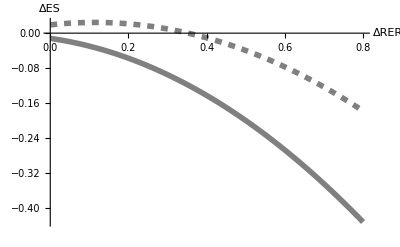

```mathematica
Plot[{-0.012-0.128 x-0.498 x^2,0.019+0.098 x-0.431 x^2},{x,0,0.8},PlotStyle->{Directive[Gray,Thickness[0.01]],Directive[Gray,Dashed,Thickness[0.01]]},AxesLabel->{"ΔRER","ΔES"}]
```

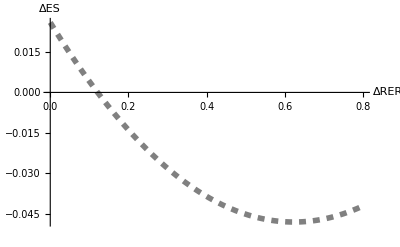

```mathematica
Plot[{.026-.238 x+.191  x^2},{x,0,0.8},PlotStyle->{Directive[Gray,Thickness[0.01]],Directive[Gray,Dashed,Thickness[0.01]]},AxesLabel->{"ΔRER","ΔES"}]
```

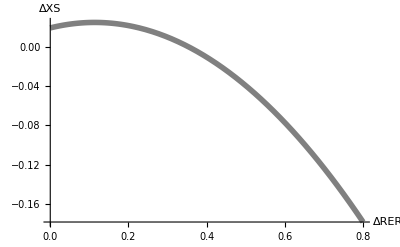

```mathematica
Plot[{.019 +.098 x -.431 x^2},{x,0,.8},PlotStyle->{Directive[Gray,Thickness[0.01]]},
AxesLabel->{"Δrer","Δxs"},AxesOrigin->{0,.019 +.098 x -.431 x^2/.x->.8}]
```

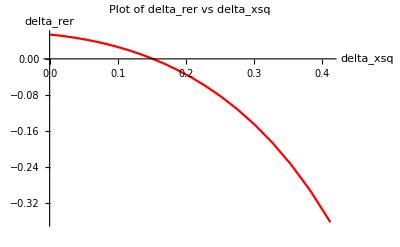

```mathematica
deltarer={0.412128605,0.382731849,0.354307679,0.32697425,0.300826712,0.275840353,0.251989185,0.229293083,0.207720109,0.18723903,0.167777498,0.14935111,0.131892307,0.115301242,0.099599701,0.084660688,0.070510915,0.05707018,0.044265464,0.032095778,0.020527675,0.009498894,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5,-3.08499*10^-5};
deltaxsq={-0.362400455,-0.292356998,-0.234283685,-0.18598055,-0.145742666,-0.112150788,-0.084072084,-0.060558641,-0.040845866,-0.024288433,-0.010368481,0.001342082,0.011209068,0.019512834,0.026518415,0.032425329,0.037404006,0.04158457,0.045093144,0.048039574,0.050497876,0.052545618,0.053943733,0.052564159,0.0512486,0.050001837,0.048814296,0.047681856,0.046600768,0.045565591,0.044577344,0.043631055,0.042724107,0.041854097,0.041015707,0.040213229,0.039441549,0.038698929,0.037985019,0.037295758,0.036628575,0.035987245,0.035367987,0.034769681,0.034191281,0.033629703,0.033088313,0.032565016,0.032057106,0.031564796,0.031087378,0.030622434,0.030172894,0.029736362,0.029312281,0.028900126,0.028498603,0.02810886,0.027729634,0.027360504,0.027001073,0.026649628,0.026308515,0.025976024,0.025651832,0.02533621,0.025027698,0.024725457,0.024431552,0.024144553,0.023864219,0.023590319,0.023321609,0.023059955,0.022804577,0.022554335,0.022309524,0.02206905,0.021834606,0.021605091,0.021380351,0.021160238,0.020944611,0.020732521,0.020525863,0.02032291,0.02012393,0.01992881};

(*Pair the x and y values using Transpose*)
data=Transpose[{Take[deltarer,23],Take[ deltaxsq,23]}];

(*Create the ListPlot*)ListPlot[data,PlotStyle->Red,AxesLabel->{"delta_xsq","delta_rer"},PlotLabel->"Plot of delta_rer vs delta_xsq", Joined->True]
```

```mathematica
data
```

{datarer,dataxsq}